The most relevant code is included in the homework, this is just for your convenience if you want to see more of what is specifically going on.

```mathematica
ℰ=a/2(T-Subscript[T, 0])ϕ^2+Subscript[λ, 4]/4 ϕ^4+Subscript[λ, 6]/6 ϕ^6;
noTrules={Subscript[T, 0]->1/2,a->1,Subscript[λ, 6]->10}; (* General Parameter Vals *)
part1rules=noTrules~Join~{Subscript[λ, 4]->-5};  (*With Subscript[λ, 4] < 0*)
part2rules=noTrules~Join~{Subscript[λ, 4]->5};  (*With Subscript[λ, 4] > 0*)
rules1=part1rules~Join~{T->2}; (* One Temperature *)
rules2=part1rules~Join~{T->0}; (* Another Temperature *)
rules3=part2rules~Join~{T->2};
rules4=part2rules~Join~{T->0}; 
extremalℰ=(ℰ/.{T-Subscript[T, 0]->dT}/.(Solve[D[ℰ/.{T-Subscript[T, 0]->dT},ϕ]==0,ϕ])//Simplify);
dTsoln=Solve[0==extremalℰ[[2]],dT][[2,1]]//Quiet;
Tc=(Subscript[T, 0]+dT/.dTsoln)/.part1rules;
```

```mathematica
img1=Manipulate[
Plot[{ℰ/.rules1,ℰ/.rules2,ℰ/.part1rules/.T->t},{ϕ,-1,1},
(* Make the Plot Look nice *)
PlotRange->{{-1,1},{-0.3,0.5}},
ImageSize->Large,
AxesLabel->{Style["ϕ̃",Bold,14],Style["ℰ[ϕ̃]",Bold,14]},
PlotLabel->Style[StringForm["a=``, T_0=``, λ_4=``, λ_6=``",N@a/.part1rules,N@Subscript[T, 0]/.part1rules,N@Subscript[λ, 4]/.part1rules,N@Subscript[λ, 6]/.part1rules],Bold,16],
PlotLegends->{"T=2.0","T=0.0","T="<>ToString[N[t,3]]}
],{{t,Tc,"Temperature"},0,3,0.1},
FrameLabel->{{"",""},{"",Style["Behavior Above/Below/At T_c",Bold,16]}} ]
```

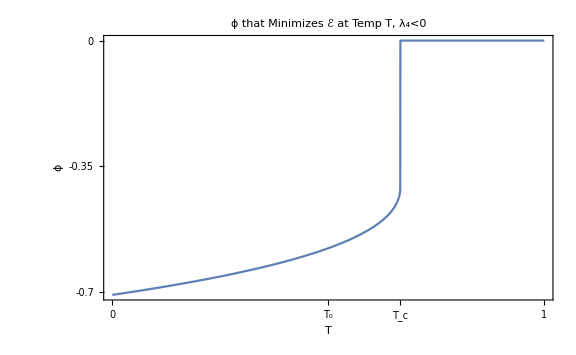

```mathematica
img2=Plot[Min[ϕ/.Solve[D[ℰ/.part1rules,ϕ]==0,ϕ,Reals]],{T,0,1},
PlotLabel->"ϕ that Minimizes ℰ at Temp T, λ_4<0",
AxesLabel->{"T","ϕ"},ImageSize->Large,
Frame->True,
FrameTicks->{{0,{0.5,Subscript[T, 0]},{Tc,Subscript[T, c]},1},{-0.7,-0.35,0}}]
```

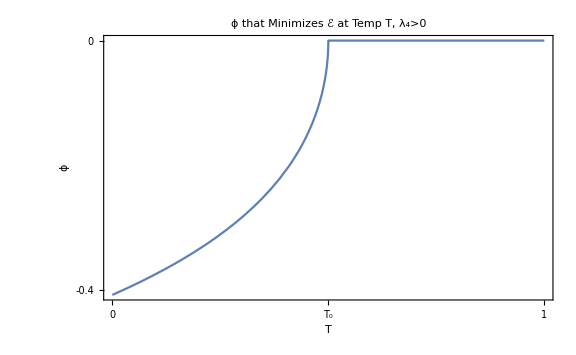

```mathematica
img3=Plot[Min[ϕ/.Solve[D[ℰ/.part2rules,ϕ]==0,ϕ,Reals]],{T,0,1},
PlotLabel->"ϕ that Minimizes ℰ at Temp T, λ_4>0",
AxesLabel->{"T","ϕ"},ImageSize->Large,
Frame->True,
FrameTicks->{{0,{0.5,Subscript[T, 0]},1},{-0.4,0}}]
```

```mathematica
img4=Manipulate[
Plot[{ℰ/.rules3,ℰ/.rules4,ℰ/.part2rules/.T->t},{ϕ,-1,1},
(* Make the Plot Look nice *)
PlotRange->{{-1,1},{-0.3,0.5}},
ImageSize->Large,
AxesLabel->{Style["ϕ̃",Bold,14],Style["ℰ[ϕ̃]",Bold,14]},
PlotLabel->Style[StringForm["a=``, T_0=``, λ_4=``, λ_6=``",N@a/.part2rules,N@Subscript[T, 0]/.part2rules,N@Subscript[λ, 4]/.part2rules,N@Subscript[λ, 6]/.part2rules],Bold,16],
PlotLegends->{"T=2.0","T=0.0","T="<>ToString[N[t,3]]}
],{{t,Tc,"Temperature"},0,3,0.1},
FrameLabel->{{"",""},{"",Style["Behavior Above/Below/At 'T_c'",Bold,16]}} ]
```

```mathematica
Export["~/school/SP23/PHYS202a/figs/CritPlot.png",img1]
```

~/school/SP23/PHYS202a/figs/CritPlot.png

```mathematica
Export["~/school/SP23/PHYS202a/figs/l4l0.png",img2]
```

~/school/SP23/PHYS202a/figs/l4l0.png

```mathematica
Export["~/school/SP23/PHYS202a/figs/l4g0.png",img3]
```

~/school/SP23/PHYS202a/figs/l4g0.png

```mathematica
Export["~/school/SP23/PHYS202a/figs/NotCritPlot.png",img4]
```

~/school/SP23/PHYS202a/figs/NotCritPlot.png

```mathematica
(*Use dT instead of T-Subscript[T, 0]*)
free1=ℰ/.{T-Subscript[T, 0]->dT}/.part1rules;
(*Find Possible minima by setting derivative = 0*)
SolvePossibleExtrema1[ddT_]:=Solve[0==D[free1/.part1rules,ϕ]/.dT->ddT,Reals]
(*Plug those values into the free energy*)
extremalenergies1[T_]:=free1/.SolvePossibleExtrema1[T]//FullSimplify;
Table[{t,Min@extremalenergies1[t]/.dT->t},{t,-0.4,0.4,0.1}]//ColumnForm
(*Table[Min@(ϕ/.PossibleExtrema1/.dT->t),{t,-1,10,0.1}]*)
```

{-0.4,-0.100642}
{-0.3,-0.0776416}
{-0.2,-0.0561401}
{-0.1,-0.036332}
{0.,-0.0185185}
{0.1,-0.00326835}
{0.2,0}
{0.3,0}
{0.4,0}

```mathematica
(*Use dT instead of T-Subscript[T, 0]*)
free2=ℰ/.{T-Subscript[T, 0]->dT}/.part2rules;
(*Find Possible minima by setting derivative = 0*)
SolvePossibleExtrema2[ddT_]:=Solve[0==D[free2/.part2rules,ϕ]/.dT->ddT,Reals]
(*Plug those values into the free energy*)
extremalenergies2[T_]:=free2/.SolvePossibleExtrema2[T]//FullSimplify;
Table[{t,Min@extremalenergies2[t]/.dT->t},{t,-0.4,0.4,0.1}]//ColumnForm
(*Table[Min@(ϕ/.PossibleExtrema1/.dT->t),{t,-1,10,0.1}]*)
```

{-0.4,-0.0154564}
{-0.3,-0.00912311}
{-0.2,-0.00428822}
{-0.1,-0.00114683}
{0.,0}
{0.1,0}
{0.2,0}
{0.3,0}
{0.4,0}

{0,((λ_4+√(λ_4^2-4 a dT λ_6)) (λ_4^2-8 a dT λ_6+λ_4 √(λ_4^2-4 a dT λ_6)))/(48 λ_6^2),((λ_4+√(λ_4^2-4 a dT λ_6)) (λ_4^2-8 a dT λ_6+λ_4 √(λ_4^2-4 a dT λ_6)))/(48 λ_6^2),((-λ_4+√(λ_4^2-4 a dT λ_6)) (-λ_4^2+8 a dT λ_6+λ_4 √(λ_4^2-4 a dT λ_6)))/(48 λ_6^2),((-λ_4+√(λ_4^2-4 a dT λ_6)) (-λ_4^2+8 a dT λ_6+λ_4 √(λ_4^2-4 a dT λ_6)))/(48 λ_6^2)}

```mathematica
Solve[((Subscript[λ, 4]+√(Subscript[λ, 4]^2-4 a dT Subscript[λ, 6])) (Subscript[λ, 4]^2-8 a dT Subscript[λ, 6]+Subscript[λ, 4] √(Subscript[λ, 4]^2-4 a dT Subscript[λ, 6])))/(48 Subscript[λ, 6]^2)==0,dT]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{dT→0},{dT→(3 λ_4^2)/(16 a λ_6)}}

```mathematica
Subscript[λ, 4]^2==Subscript[λ, 4]^2-4 a dT Subscript[λ, 6]
```